```mathematica
EventHandler[InputField[],{"KeyDown","q"}:>EmitSound[Sound[SoundNote["C5",.2,"Gunshot"]]],{"KeyDown","w"}:>EmitSound[Sound[SoundNote["B",1,"Taiko"]]],{"KeyDown","e"}:>EmitSound[Sound[SoundNote["A",.2,"Woodblock"]]],{"KeyDown","r"}:>EmitSound[Sound[SoundNote["G",1,"Taiko"]]],{"KeyDown","t"}:>EmitSound[Sound[SoundNote["F",1,"Taiko"]]],{"KeyDown","y"}:>EmitSound[Sound[SoundNote["E",1,"Taiko"]]],{"KeyDown","u"}:>EmitSound[Sound[SoundNote["D",1,"Taiko"]]],{"KeyDown","i"}:>EmitSound[Sound[SoundNote["C",1,"Taiko"]]],{"KeyDown","o"}:>EmitSound[Sound[SoundNote["B3",1,"Taiko"]]],{"KeyDown","p"}:>EmitSound[Sound[SoundNote["A3",1,"Taiko"]]],{"KeyDown","a"}:>EmitSound[Sound[SoundNote["G3",1,"Taiko"]]],{"KeyDown","s"}:>EmitSound[Sound[SoundNote["F3",1,"Taiko"]]],{"KeyDown","d"}:>EmitSound[Sound[SoundNote["E3",1,"Taiko"]]],{"KeyDown","f"}:>EmitSound[Sound[SoundNote["D3",1,"Taiko"]]],{"KeyDown","g"}:>EmitSound[Sound[SoundNote["C3",1,"Taiko"]]]]
```

```mathematica
EventHandler[
InputField[]
,
{"KeyDown","q"}:>EmitSound[Sound[Table[SoundNote[i,0.1,115],{i,0,40}]]]
,
{"KeyDown","w"}:>EmitSound[Sound[Table[SoundNote[40-j,0.1,"Echoes"],{j,0,40}]]]
]
```

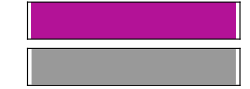

```mathematica
Sound[
SoundNote[Range[64],15,"Whistle"]
]
```

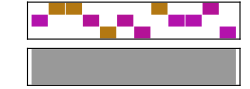

```mathematica
Sound[SoundNote[#,1,RandomChoice[{"Echoes","Whistle","Violin"}]]& /@ RandomInteger[
RandomChoice[{2,4,6,8,24}],
 RandomChoice[{10,12,14,16,18}]],
 RandomChoice[{2,4,6,8,16}]]
```